```mathematica
Remove["Global`*"];
```

```mathematica
fp={{0.50006,-12019.47},{0.5511,-8352.63},{0.59989,-5963.33},{0.64981,-4354.21},{0.69972,-3125.42},{0.75189,-2296.48},{0.79955,-1516.3},{0.85173,-1106.71},{0.90051,-687.36},{0.95269,-511.82},{0.99944,-4.7},{1.05026,131.83},{1.10017,229.35},{1.15009,365.88},{1.20226,453.65},{1.25015,726.71},{1.30096,912.01},{1.34998,1233.83},{1.39989,1506.89},{1.44868,1740.95},{1.50085,1965.25}}
```

{{0.50006,-12019.5},{0.5511,-8352.63},{0.59989,-5963.33},{0.64981,-4354.21},{0.69972,-3125.42},{0.75189,-2296.48},{0.79955,-1516.3},{0.85173,-1106.71},{0.90051,-687.36},{0.95269,-511.82},{0.99944,-4.7},{1.05026,131.83},{1.10017,229.35},{1.15009,365.88},{1.20226,453.65},{1.25015,726.71},{1.30096,912.01},{1.34998,1233.83},{1.39989,1506.89},{1.44868,1740.95},{1.50085,1965.25}}

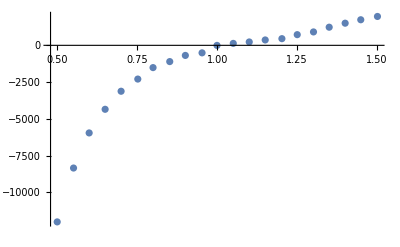

```mathematica
gp=ListPlot[fp]
```

```mathematica
K=10000;
```

```mathematica
FindFit[fp,{2/(3 Subscript[λ, 1])(Subscript[u, 1](Subscript[λ, 1]^(2/3(1-Subscript[b, 1])Subscript[α, 1])-Subscript[λ, 1]^(1/3(Subscript[b, 1]-1)Subscript[α, 1]))+Subscript[u, 2](Subscript[λ, 1]^(2/3(1-Subscript[b, 1])Subscript[α, 2])-Subscript[λ, 1]^(1/3(Subscript[b, 1]-1)Subscript[α, 2])))+1/2 K (Subscript[λ, 1]^(1+4 Subscript[b, 1])+Subscript[λ, 1]^-1),{-100000<=Subscript[u, 1]≤10000,-1000<=Subscript[u, 2]≤1000,-100<=Subscript[α, 1]≤100,-10<=Subscript[α, 2]≤10,-0.55<=Subscript[b, 1]≤-0.45}},{Subscript[u, 1],Subscript[u, 2],Subscript[α, 1],Subscript[α, 2],Subscript[b, 1]},Subscript[λ, 1]]
```

{u_1→10000.,u_2→-1000.,α_1→0.828387,α_2→-4.45358,b_1→-0.45}

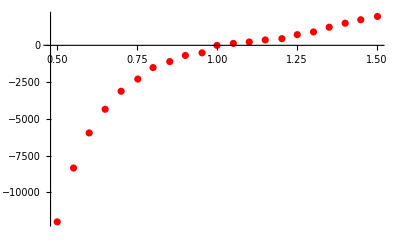

```mathematica
Show[ListPlot[fp,PlotStyle->Red],Plot[{(2 (Subscript[u, 1] (Subscript[λ, 1]^(2/3 (1-Subscript[b, 1]) Subscript[α, 1])-Subscript[λ, 1]^(1/3 (Subscript[b, 1]-1) Subscript[α, 1]))+Subscript[u, 2] (Subscript[λ, 1]^(2/3 (1-Subscript[b, 1]) Subscript[α, 2])-Subscript[λ, 1]^(1/3 (Subscript[b, 1]-1) Subscript[α, 2]))))/(3 Subscript[λ, 1])+1/2 K (Subscript[λ, 1]^(1+4 Subscript[b, 1])+1/Subscript[λ, 1]),{-100000≤Subscript[u, 1]≤10000,-1000≤Subscript[u, 2]≤1000,-100≤Subscript[α, 1]≤100,-10≤Subscript[α, 2]≤10,-0.55≤Subscript[b, 1]≤-0.45}}/.{Subscript[u, 1]->9999.999999998296,Subscript[u, 2]->-999.9999999999545,Subscript[α, 1]->0.8283865026329761,Subscript[α, 2]->-4.453580822684346,Subscript[b, 1]->-0.4500000000005173},{Subscript[λ, 1],0.50006,1.50085}]]
```